9.81

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-3.13209 √R},{v→3.13209 √R}}

3.13209 √R

{{H→2.5 R}}

2.5 R

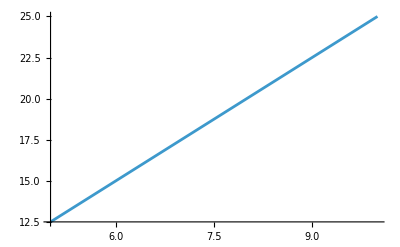

```mathematica
ClearAll["Global`*"]
g=9.81
(*warunek w najwyższym punkcie [siła odśrodkowa = siła grawitacji]*)
rown1=Solve[(m*v^2)/R==m*g,v]
vs=v/.rown1[[2]]
(*zasada zachowania energii*)
rown2=Solve[m*g*H==2*m*g*R+1/2 m*vs^2,H]
H[R_]=H/.rown2[[1]]
Plot[H[R],{R,5,10}]
```